## ReadMe

This Mathematica notebook  contains some useful functions to perform a traditional analysis (i.e. using cuts of kinematic variables) of collider events in the LHC Olympics (LHCO) format, simulated using MadGraph (with Pythia and Delphes).  All numbers are in pb (picobarns), pb^-1 (inverse picobarns) or GeV. The first two sections contain functions that can be used to handle .lhco files produced by MadGraph. The last section shows a quick example of how to use some of these functions to extract parts of the parameter space where signal events can be seen, calculate signal over noise ratio (SNR) and plot histograms of signal and background events. The demonstrated example has 1 signal and 3 backgrounds.

The code here was used by the Cornell Particle Theory group, and much of it is due to Prof. Maxim Perelstein (my Ph.D. advisor). I have updated some of it, and added a lot of my own functions. It was not written with public dissemination in mind, and documentation is not great. However, I hope that any particle physicist can make sense of what the code does. Note that some of these functions may not be useful for v5 of MadGraph_aMC@NLO, which supersedes previous versions. 

This notebook is not actively being maintained or updated. Please email me at gowri.kurup@gmail.com if you run into any issues.

## General Functions

```mathematica
ClearAll[particle,finout];

(* For PDG numbers, see e.g. http://home.fnal.gov/~maeshima/alignment/ORCA/PYTHIA_particle_codes.ps *)

particle[2] =u;
particle[-2] =uBar;

particle[1] =d;
particle[-1] =dBar;

particle[3] ="s";
particle[-3] ="sBar";

particle[4] ="c";
particle[-4] ="cBar";

particle[5] =b;
particle[-5] =bBar;

particle[6] =t;
particle[-6] =tBar;

particle[11] =SuperMinus[e];
particle[-11] =SuperPlus[e];

particle[12] ="⋁_e ";
particle[-12] ="(⋁_e)^c";

particle[13] ="μ^-";
particle[-13]="μ^+";

particle[14] ="⋁_μ ";
particle[-14] ="(⋁_μ)^c";

particle[16] ="⋁_τ ";
particle[-16] ="(⋁_τ)^c";

particle[21] =gluon;

particle[23] = Z;

particle[24] =SuperPlus[W];
particle[-24] =SuperMinus[W];

particle[1000006] =Subscript[OverTilde[t], 1];
particle[-1000006] =SuperStar[Subscript[OverTilde[t], 1]];
particle[1000022] =Subscript[OverTilde[χ], 0];

finout[-1] = in;
finout[1] = out;
finout[2]  = decayed;
```

```mathematica
ReadME[rawInput_ ] := Module[{pos1, pos2},

pos1=Position[rawInput,{"<event>"}];
pos2=Position[rawInput,{"<mgrwt>"}];

Print["No. of events: ",Length[pos1]];

(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
Table[Take[rawInput,{pos1[[j,1]]+2,pos2[[j,1]]-1}] ,{j,1,Length[pos1]}]

];
```

```mathematica
EventPrint[ event_ ] := ( Print[Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel}}, event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13}]//MatrixForm]);
```

```mathematica
ReadEventsPythia[filename_]:=Module[{eventListp, eventListOutLp},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadMEPythia[testp]; ]; 
(*convert raw data into chameleon-readable form*)
eventListp = eventListp[[1;;(Length[eventListp]-1)]];
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info -- boring for e+e- collider*)
ClearMemory;
{eventListp, eventListOutLp}
];
```

```mathematica
ReadMEPythia[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"<event>"}][[1,1]]; 
(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
pythiaout=DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{"<event>"}|{"</LesHouchesEvents>"}| {"</event>"} | eventInfo,2];
ClearMemory;
pythiaout
);
```

```mathematica
(*Give this function the filename of a PGS output file and it gives you an eventlist in the same format as MGME output*)
ReadPGSEventsAsMGME[filename_]:=ReadPGSEventFile[filename]//ConvertPGSeventstoMGMEevents;
```

```mathematica
(*Give this function the filename of the PGS output file and it'll give you a list of events. Use PGSEventPrint to show a single event*)
ReadPGSEventFile[filename_]:=Module[{SplitData,PGSreadfile,found,entry,entryTableHeading,numevents,PGSeventlist},

SplitData[rawObjList_]:=Split[Drop[rawObjList,If[NumberQ[rawObjList[[1,1]]],0,1]],Less[First[#1],First[#2]]&];

PGSreadfile=SplitData[Import[filename,"Table"]];



(* Find the entry in the read table where the table starts, i.e. table header. After that it's normal PGS events.*)
found=False;
entry = 0;
While[found==False&&entry<  Length[PGSreadfile],
entry++;
If[PGSreadfile[[entry]]=={{"#","typ","eta","phi","pt","jmas","ntrk","btag","had/em","dum1","dum2"}},
found=True;];
];
If[entry ≥  Length[PGSreadfile], entry=0];
entryTableHeading = entry;

(*get total number of events*)
numevents = Length[PGSreadfile]-entryTableHeading;
(*store list of PGS events*)
PGSeventlist = Table[Drop[PGSreadfile[[entryTableHeading+eventindex]],1],{eventindex,1,numevents}];
ClearMemory;
PGSeventlist
];
```

```mathematica
PGSEventPrint[PGSevent_]:=Join[{{"#","typ","eta","phi","pt","jmas","ntrk","btag","had/em","dum1","dum2"}}, PGSevent]//MatrixForm//Print;
```

```mathematica
(*Give this function a list of PGS events that have been read by ReadPGSEventFile and it outputs a list of events that is in the same format as the MGME events*)
ConvertPGSeventstoMGMEevents[PGSevents_]:=Module[{output}, 
output = Table[PGSevents[[eventindex]][[particleindex]]//ConvertPGSparticletoMGMEparticle,{eventindex,1,Length[PGSevents]},{particleindex,1,Length[PGSevents[[eventindex]]]}];
ClearMemory[];
output
];
```

```mathematica
(*use these pointers to access entries of a single PGS event*)
typePGSINDEX = 2;
etaPGSINDEX = 3;
phiPGSINDEX = 4;
ptPGSINDEX = 5;
jmasPGSINDEX = 6;
ntrkPGSINDEX=7;
btagPGSINDEX=8;
```

```mathematica
ConvertPGSparticletoMGMEparticle[PGSparticle_]:=Module[{currenttype,currenteta,currentphi,currentpt,currentjmas,currentntrk,currentbtag,currentpx,currentpy,currenttheta,currentpz,currentPID},
(*load parameters of this particle into *)
currenttype = PGSparticle[[typePGSINDEX]];
currenteta = PGSparticle[[etaPGSINDEX]];
currentphi = PGSparticle[[phiPGSINDEX]];
currentpt = PGSparticle[[ptPGSINDEX]];
currentjmas = PGSparticle[[jmasPGSINDEX]];
currentntrk = PGSparticle[[ntrkPGSINDEX]];
currentbtag=PGSparticle[[btagPGSINDEX]];



currentpx = currentpt Cos[currentphi];
currentpy = currentpt Sin[currentphi];

currenttheta = 2 ArcTan[Exp[-currenteta]];

currentpz = currentpt/Tan[currenttheta];


(*note we are discarding some τ information here -- namely, whether it decayed via three prongs (ntrk = ± 3) or one prong (ntrk = ± 1)*)
(*we are also discarding whether the tagged b was tight (btag = 2) or loose (btag = 1)*)
Which[
(*photon*)
currenttype==0, currentPID = 22,
(*e+*)
currenttype==1&&currentntrk==1, currentPID = -11,
(*e-*)
currenttype==1&&currentntrk==-1, currentPID = 11,
(*μ+*)
currenttype==2&&currentntrk==1, currentPID = -13,
(*μ-*)
currenttype==2&&currentntrk==-1, currentPID = 13,
(*τ+*)
currenttype==3&&currentntrk>0, currentPID = -15,
(*τ-*)
currenttype==3&&currentntrk<0, currentPID = 15,
(*b*)
currenttype==4&&currentbtag>0, currentPID = 5,
(*other jet: label as gluon*)
currenttype ==4 && currentbtag==0, currentPID= 21,
(*MET: label as electron-neutrino*)
currenttype==6, currentPID = 12
];


{currentPID,1,0,0,0,0,currentpx,currentpy,currentpz,√(currentpx^2+currentpy^2+currentpz^2),currentjmas,0,0}
];
```

```mathematica
ReadPGSEventFileAsMGME[filename_]:=Module[{temp},
temp=ReadPGSEventFile[filename];
ConvertPGSparticletoMGMEparticle[temp]
];
```

```mathematica
ScatteringCrossSection[rawInput_]:=ToExpression[StringReplace[Last[StringSplit[FindList[rawInput,"Integrated weight",1][[1]]]],"e"->"*10^"]]*10^3
```

```mathematica
(* those are input or decayed particles*)
decayedOrIn = {_,-1,_,_,_,_,_,_,_,_,_,_,_}  | {_,2,_,_,_,_,_,_,_,_,_,_,_};

EventOut[ event_ ]  := (DeleteCases[event,decayedOrIn]);

SetOut[ event_ ]  := (DeleteCases[event,decayedOrIn,2]);
```

```mathematica
EffMassAll[objList_]  :=Plus @@ Map[ptOf,objList//Transpose,{2}]; 

EffMass[event_]  :=Plus @@ Map[ptOf,event,{1}];

pT[event_]  :=Map[ptOf,event,{1}]//Flatten;
eta[event_] := Map[etaOf,event,{1}]//Flatten;
theta[event_] := Map[thetaOf,event,{1}]//Flatten;
threeVector[event_] := Map[ThreeVectorFrom,event,{1}];


ptOf[{_,_,_,_,_,_,px_,py_,___}]:=√(px^2+py^2);
enOf[{_,_,_,_,_,_,_,_,_,En_,___}]:=En;
thetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcCos[pz/√(px^2+py^2+ pz^2)];
etaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:=- Log[ Abs[Tan[ ArcCos[pz/√(px^2+py^2+ pz^2)]/2]]]; 
FourVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,En_,___}] := {En, px, py,pz };

FourLength[{pe_,pz_,px_,py_}] := Sqrt[Max[pe^2- px^2 - py^2 - pz^2 ,0.0]];

ThreeVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,___}] := { px, py,pz };

CosthetaTwoJet[{jet1_,jet2_}] := (a = ThreeVectorFrom[jet1]; b=  ThreeVectorFrom[jet2]; a.b/√(a.a b.b));

GetAll[evt_]:=evt;
all[evt_]:=True;

Freq[evtList_,crit_,objsel_,plotfunc_,{min_,max_,nbins_}]:=BinCounts[ Flatten[ plotfunc/@Flatten4[objsel/@Select[evtList,crit]]],{min,max,(max-min)/nbins}];

Flatten4[List_]:=Flatten[List,Max[0,Depth[List]-4]]; 

oJetlhe=  {2,1,_,_,_,_,_,_,_,_,_,_,_}  | {-2,1,_,_,_,_,_,_,_,_,_,_,_}|{21,1,_,_,_,_,_,_,_,_,_,_,_}  ;

oMissingEnergy = {8888,1,_,_,_,_,_,_,_,_,_,_,_}  ;

PTSort[event_]:=Sort[event,Greater[ptOf[#1],ptOf[#2]]&];
```

```mathematica
{pidIndex , inoutIndex,mother1Index ,mother2Index,color1Index, color2Index, pxIndex, pyIndex, pzIndex, p0Index, massIndex, sixIndex, helIndex, tagindex, reconindex, combindex, MCreconindex} = {1,2,3,4,5,6,7,8,9,10,11,12,13, 14,15, 16, 17};
invisiblelist={12,-12,14,-14,16,-16};
jetlist={1,-1,2,-2,3,-3,4,-4,5,-5,21};
leptonlist={11,-11,13,-13,15,-15};
```

```mathematica
nJets[event_]:=Length[Select[event,MemberQ[jetlist, #[[pidIndex]]]&]]
nLeps[event_]:=Length[Select[event,MemberQ[leptonlist, #[[pidIndex]]]&]]
```

```mathematica
(* Finds total visible pT (magnitude and vector) from an OUT-event *)
TotalVisiblepT[event_]:=Module[{visiblept, currentparticle, i},
visiblept = {0,0};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[!MemberQ[invisiblelist, currentparticle[[pidIndex]]],
visiblept =  {currentparticle[[pxIndex]],currentparticle[[pyIndex]]} + visiblept;
];
];
√(visiblept[[1]]^2+visiblept[[2]]^2)
];
```

```mathematica
VisiblepT[event_]:=Module[{visiblept, currentparticle, i},
visiblept = {0,0};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[!MemberQ[invisiblelist, currentparticle[[pidIndex]]],
visiblept =  {currentparticle[[pxIndex]],currentparticle[[pyIndex]]} + visiblept;
];
];
visiblept
];
```

```mathematica
TotalInvMass[event_]:=Module[{p,i},
p = {0,0,0,0};
For[i = 1, i≤Length[event],i++,
p+=FourVectorFrom[event[[i]]]];
FourLength[p]
];
```

```mathematica
TotalJetInvMass[event_]:=Module[{p,currentparticle,i},
p = {0,0,0,0};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],p+=FourVectorFrom[event[[i]]]]];
FourLength[p]
];
```

```mathematica
TotalLeptonInvMass[event_]:=Module[{p,currentparticle,i},
p = {0,0,0,0};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[leptonlist, currentparticle[[pidIndex]]],p+=FourVectorFrom[event[[i]]]]];
FourLength[p]
];
```

```mathematica
(* Simplest Histogram *)
ShowHistogram[listS_,listB_,fn_,n_,bin_]:=Module[{dataS,dataB},
If[n>0,
{dataS=Map[fn[#[[n]]]&,listS];
dataB=Map[fn[#[[n]]]&,listB]},
{dataS=Map[fn[#]&,listS];
dataB=Map[fn[#]&,listB]}];Show[Histogram[{dataS,dataB},{bin},Probability,BaseStyle->FaceForm[None],ChartStyle->{EdgeForm[{Thick,Red}],EdgeForm[{Thick,Blue}]}],Filling->Axis, Frame->True,FrameStyle->Thickness[0.002]]
]
```

```mathematica
(* Fancy Histogram with 3 backgrounds, TeX type using MaTeX, which needs to be installed *)
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->14};

ShowHistogram[listS_,listB1_,listB2_,listB3_,fn_,labelx_,bins_]:=Module[{dataS,dataB1,dataB2,dataB3,countBorderS,countBorderB1,countBorderB2,countBorderB3},
dataS=Map[fn[#]&,listS];
dataB1=Map[fn[#]&,listB1];
dataB2=Map[fn[#]&,listB2];
dataB3=Map[fn[#]&,listB3];
countBorderS=Partition[Riffle[Riffle[#1,#1[[2;;]]],Riffle[#2,#2]],2]&@@HistogramList[dataS,bins,"Probability"];
countBorderB1=Partition[Riffle[Riffle[#1,#1[[2;;]]],Riffle[#2,#2]],2]&@@HistogramList[dataB1,bins,"Probability"];
countBorderB2=Partition[Riffle[Riffle[#1,#1[[2;;]]],Riffle[#2,#2]],2]&@@HistogramList[dataB2,bins,"Probability"];
countBorderB3=Partition[Riffle[Riffle[#1,#1[[2;;]]],Riffle[#2,#2]],2]&@@HistogramList[dataB3,bins,"Probability"];
Show[
ListLinePlot[countBorderS,PlotStyle->Directive[Thickness[0.003],Red],PlotRange->All],ListLinePlot[countBorderB1,PlotStyle->Directive[Thickness[0.003],Blue],PlotRange->All],
ListLinePlot[countBorderB2,PlotStyle->Directive[Thickness[0.003],Purple],PlotRange->All],
ListLinePlot[countBorderB3,PlotStyle->Directive[Thickness[0.003],Orange],PlotRange->All],
PlotRangePadding->0,Frame->True,FrameStyle->BlackFrame,PlotRange->{{bins[[1]],bins[[2]]},{0,1.1*Max[countBorderS[[All,2]],countBorderB1[[All,2]],countBorderB1[[All,2]],countBorderB3[[All,2]]]}},
FrameLabel->{MaTeX[labelx,Magnification->1.5],MaTeX["\\mathrm{Events\\ normalised\\ to\\ 1}",Magnification->1.5]},
BaseStyle->texStyle,TicksStyle->texStyle]
]
```

## Specific Functions for Clockwork Neutrino Analysis

```mathematica
mljjMax[event_]:=Module[{temp,m,leps,jets,i,j},
m=0;
jets=Subsets[Select[event,MemberQ[jetlist, #[[pidIndex]]]&],{2}];
leps=Select[event,MemberQ[leptonlist, #[[pidIndex]]]&];
For[i = 1, i≤Length[leps],i++,
For[j = 1, j≤Length[jets],j++,
temp=FourLength[FourVectorFrom[leps[[i]]]+FourVectorFrom[jets[[j,1]]]+FourVectorFrom[jets[[j,2]]]];
If[temp≥m,m=temp];
]];
m
];
```

```mathematica
mljjMin[event_]:=Module[{temp,m,leps,jets,i,j},
m=10000;
jets=Subsets[Select[event,MemberQ[jetlist, #[[pidIndex]]]&],{2}];
leps=Select[event,MemberQ[leptonlist, #[[pidIndex]]]&];
For[i = 1, i≤Length[leps],i++,
For[j = 1, j≤Length[jets],j++,
temp=FourLength[FourVectorFrom[leps[[i]]]+FourVectorFrom[jets[[j,1]]]+FourVectorFrom[jets[[j,2]]]];
If[temp≤m,m=temp];
]];
m
];
```

```mathematica
mjj[event_]:=Module[{jets,jetSort,i},
jets=Select[event,MemberQ[jetlist, #[[pidIndex]]]&];
jetSort=Reverse[SortBy[jets,√((#[[pxIndex]])^2+(#[[pyIndex]])^2)&]];
FourLength[FourVectorFrom[jetSort[[1]]]+FourVectorFrom[jetSort[[2]]]]
];
```

```mathematica
mll[event_]:=Module[{leps,lepSort,o},
leps=Select[event,MemberQ[leptonlist, #[[pidIndex]]]&];
If[Length[leps]>1,
{lepSort=Reverse[SortBy[leps,√((#[[pxIndex]])^2+(#[[pyIndex]])^2)&]];
o=FourLength[FourVectorFrom[lepSort[[1]]]+FourVectorFrom[lepSort[[2]]]]},
o=FourLength[FourVectorFrom[leps[[1]]]]];
o
];
```

```mathematica
pTj[event_]:=Module[{jets,jetpT,i},
jets=Select[event,MemberQ[jetlist, #[[pidIndex]]]&];
jetpT=Table[√((jets[[i]][[pxIndex]])^2+(jets[[i]][[pyIndex]])^2),{i,1,Length[jets]}];
Max[jetpT]
];
```

```mathematica
pTl[event_]:=Module[{leps,leppT,i},
leps=Select[event,MemberQ[leptonlist, #[[pidIndex]]]&];
leppT=Table[√((leps[[i]][[pxIndex]])^2+(leps[[i]][[pyIndex]])^2),{i,1,Length[leps]}];
Max[leppT]
];
```

## Signal and Background Analysis

```mathematica
sigDir="C:/Users/Gowri.Kurup/Documents/Clockwork/MadGraph/sig";
bkgDir="C:/Users/Gowri.Kurup/Documents/Clockwork/MadGraph/bkg";
```

```mathematica
SetDirectory[sigDir];
sigOut=ReadPGSEventsAsMGME["sig_20_99_GeV_14_TeV_universal.lhco"];
SetDirectory[bkgDir];
bkg1Out=ReadPGSEventsAsMGME["bkg_1_14_TeV.lhco"];
bkg1Out=ReadPGSEventsAsMGME["bkg_2_14_TeV.lhco"];
bkg1Out=ReadPGSEventsAsMGME["bkg_3_14_TeV.lhco"];
```

```mathematica
sig=Select[sigOut,(nJets[#]>1&&nLeps[#]>0)&];
bkg1=Select[bkg1Out,(nJets[#]>1&&nLeps[#]>0)&];
bkg2=Select[bkg2Out,(nJets[#]>1&&nLeps[#]>0)&];
bkg3=Select[bkg3Out,(nJets[#]>1&&nLeps[#]>0)&];
ClearAll[sigOut,bkg1Out,bkg2Out,bkg3Out];
```

```mathematica
SetDirectory[sigDir];
σ=ScatteringCrossSection["sig_20_99_GeV_14_TeV_universal.lhco"]
SetDirectory[bkgDir];
σb1=ScatteringCrossSection["bkg_1_14_TeV.lhco"]
σb2=ScatteringCrossSection["bkg_2_14_TeV.lhco"]
σb3=ScatteringCrossSection["bkg_3_14_TeV.lhco"]
L=3000; (* Luminosity *)
Print["No. of signal events = ",σ*L]
```

```mathematica
CutpTl=0; Cutmjj={40,120};Cutmljj1={60,180};Cutmljj2={60,150}; Cutmll={80,100}; CutTotpT=50;

sig2=Select[sig,(pTl[#]>CutpTl&& mjj[#]>Cutmjj[[1]]&&mjj[#]<Cutmjj[[2]]&&mljjMax[#]>Cutmljj1[[1]]&&mljjMax[#]<Cutmljj1[[2]]
&&mljjMin[#]>Cutmljj2[[1]]&&mljjMin[#]<Cutmljj2[[2]]&&!Between[mll[#],Cutmll]&&TotalVisiblepT[#]<CutTotpT)&];

bkg12=Select[bkg1,(pTl[#]>CutpTl&& mjj[#]>Cutmjj[[1]]&&mjj[#]<Cutmjj[[2]]&&mljjMax[#]>Cutmljj1[[1]]&&mljjMax[#]<Cutmljj1[[2]]
&&mljjMin[#]>Cutmljj2[[1]]&&mljjMin[#]<Cutmljj2[[2]]&&!Between[mll[#],Cutmll]&&TotalVisiblepT[#]<CutTotpT)&];

bkg22=Select[bkg2,(pTl[#]>CutpTl&& mjj[#]>Cutmjj[[1]]&&mjj[#]<Cutmjj[[2]]&&mljjMax[#]>Cutmljj1[[1]]&&mljjMax[#]<Cutmljj1[[2]]
&&mljjMin[#]>Cutmljj2[[1]]&&mljjMin[#]<Cutmljj2[[2]]&&!Between[mll[#],Cutmll]&&TotalVisiblepT[#]<CutTotpT)&];

bkg32=Select[bkg3,(pTl[#]>CutpTl&& mjj[#]>Cutmjj[[1]]&&mjj[#]<Cutmjj[[2]]&&mljjMax[#]>Cutmljj1[[1]]&&mljjMax[#]<Cutmljj1[[2]]
&&mljjMin[#]>Cutmljj2[[1]]&&mljjMin[#]<Cutmljj2[[2]]&&!Between[mll[#],Cutmll]&&TotalVisiblepT[#]<CutTotpT)&];

{Length[sig2],Length[bkg12],Length[bkg22],Length[bkg32]}
{Length[sig2]×10^-5×L×σ,Length[bkg12]×10^-5×L×σb1+Length[bkg22]×10^-5×L×σb2+Length[bkg32]×10^-5×L×σb3}//N

Print["σ_B after cuts = ",Length[bkg12]×10^-5×σb1+Length[bkg22]×10^-5×σb2+Length[bkg32]×10^-5×σb3//N]

SNR = (Length[sig2]×10^-5×L×σ)/(√((Length[sig2]×10^-5×L×σ)+(Length[bkg12]×10^-5×L×σb1+Length[bkg22]×10^-5×L×σb2+Length[bkg32]×10^-5×L×σb3)))
```

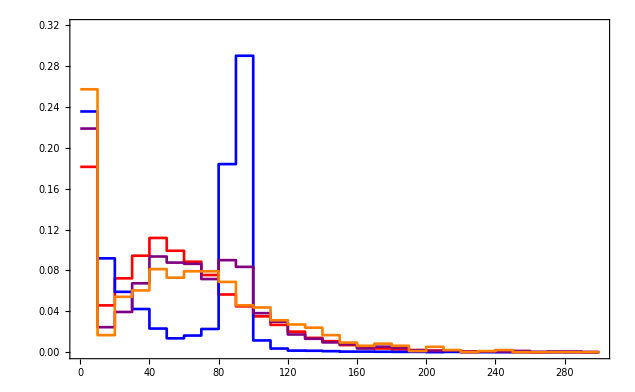

```mathematica
ShowHistogram[sig2,bkg12,bkg22,bkg32,mll,"\\mathbf{m_{ll}}",{0,300,10}]
```